Risposta libera per un sistema del II ordine che presenta una coppia di autovalori complessi e coniugati

```mathematica
A=({{1/8, -13/16}, {1/4, 3/8}})
```

{{1/8,-13/16},{1/4,3/8}}

Mi calcolo gli autovalori di A

```mathematica
λ=Eigenvalues[A]
```

{1/4 (1+ⅈ √3),1/4 (1-ⅈ √3)}

Mi calcolo il modulo e l’argomento degli autovalori (fase)

```mathematica
ρ=Abs[λ[[1]]]
```

1/2

```mathematica
θ=Arg[λ[[1]]]
```

π/3

Calcolo della matrice degli autovettori dx di A (in questo caso complessi e coniugati)

```mathematica
T=Transpose[Eigenvectors[A]]
```

{{1/2 (-1+2 ⅈ √3),1/2 (-1-2 ⅈ √3)},{1,1}}

```mathematica
MatrixForm[T]
```

(1/2 (-1+2 ⅈ √3) | 1/2 (-1-2 ⅈ √3)
1 | 1)

```mathematica
T̃=Transpose[{Re[T[[All,1]]],Im[T[[All,1]]]}]
```

{{-1/2,√3},{1,0}}

```mathematica
MatrixForm[T̃]
```

(-1/2 | √3
1 | 0)

Forma canonica Scaling-Rotation di A

```mathematica
Inverse[T̃].A.T̃
```

{{1/4,(√3)/4},{-(√3)/4,1/4}}

```mathematica
MatrixForm[Out[9]]
```

(1/4 | (√3)/4
-(√3)/4 | 1/4)

Definisco lo stato iniziale del sistema

```mathematica
Subscript[x, 0]=({{3}, {1}})
```

{{3},{1}}

e lo proietto secondo le colonne della Parte reale dell’autovettore dx di lambda e della Parte immaginaria dell’autovettore dx di lambda

```mathematica
Subscript[z, 0]=Simplify[Inverse[T̃].Subscript[x, 0]]
```

{{1},{7/(2 √3)}}

Scrivo la risposta libera

```mathematica
Subscript[x, l][k_]:=Simplify[T̃.({{ρ^k Cos[θ k], ρ^k Sin[θ k]}, {-ρ^k Sin[θ k], ρ^k Cos[θ k]}}).Subscript[z, 0]]
```

```mathematica
Subscript[x, l][k]
```

{{1/3 2^(-2-k) (36 Cos[(k π)/3]-19 √3 Sin[(k π)/3])},{1/3 2^(-1-k) (6 Cos[(k π)/3]+7 √3 Sin[(k π)/3])}}

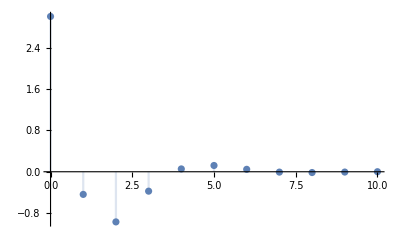

```mathematica
DiscretePlot[Subscript[x, l][k][[1]],{k,0,10},PlotRange->All]
```

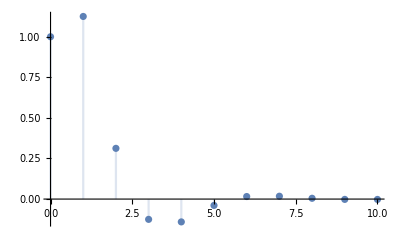

```mathematica
DiscretePlot[Subscript[x, l][k][[2]],{k,0,10},PlotRange->All]
```

```mathematica
MatrixForm[T̃]
```

(-1/2 | √3
1 | 0)